```mathematica
Clear["Global`*"]
NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"../../../../../mathematica_plot_options.nb"}]]
filename="/Users/tomoaki/BEM/H00d09_small_DT0d01_ELEMlinear_ALEpseudo_quad_ALEPERIOD1_H00d03_meshB/result.json";
filename="/Users/tomoaki/BEM/Kramer2021_DT0d01_ELEMlinear_ALEpseudo_quad_ALEPERIOD1_H00d03/result.json"
(*filename="/Users/tomoaki/BEM/Kramer2021_DT0d01_ELEMpseudo_quad_ALEpseudo_quad_ALEPERIOD1_H00d03/result.json"*)
jsonInfo[filename];
data=Import[filename];

zsurface=0.9;
d=0.3;
H0=0.1*d;
Te=0.76;
```

{plot2Doption,plot3Doption,framelabel[xlabel_String,ylabel_String,size_:20],axeslabel2D[xlabel_String,ylabel_String,size_:20],axeslabel3D[xlabel_String,ylabel_String,zlabel_String,size_:20],axeslabel[labels_List,size_: 20],importData,jsonInfo,interpolateAndFourier[time_List,disp_List,timeSpan_List: {}],interpolateAndFourierTr[timedisp_List,timeSpan_List: {}],MyFourier[list_,n_],MyInverseFourier[list_,n_],MyDiscreteConvolve[f_,g_],MyDiscreteConvolveUsingCn[FourierGF_],Rv[q_],Rs[q_],W2dQdt[q_,w_],Q2Roll[{a_,b_,c_,d_}],Q2Pitch[{a_,b_,c_,d_}],Q2Yaw[{a_,b_,c_,d_}],getOmegaFromKandDepth[k_,h_],getOmegaFromLandDepth[L_,h_],getTFromLandDepth[L_,h_],getkFromTandDepth[T_,h_]}

/Users/tomoaki/BEM/Kramer2021_DT0d01_ELEMlinear_ALEpseudo_quad_ALEPERIOD1_H00d03/result.json

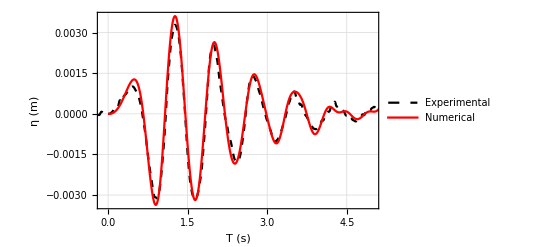

/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_bem/study_benchmark/Kramer2021/comparison_wavegauge1.eps

ブイから0.6m離れた位置における水面変位の比較

```mathematica
(*dataExp=Import[FileNameJoin["/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_bem/study_benchmark/Kramer2021/Datafile/Experimental_results/01D_CI95_Normalized.txt"],"Data"];*)
dataExp=Import[FileNameJoin["/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_bem/study_benchmark/Kramer2021/Datafile/Experimental_results/01D_Measured3_Raw.txt"],"Data"];
dataSimu=Import["/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_bem/study_benchmark/Kramer2021/Datafile/Numerical_results/FNPF1/01D_FNPF1.txt","Data"][[2;;]];

dataWG1={#1,#5}&@@@(dataExp[[2;;]]);
dataWG2={#1,#4}&@@@(dataExp[[2;;]]);

dataMyGW1=Transpose[{"simulation_time"/.data,("gauge1_intersection"/.data)[[;;,3]]}];
dataMyGW1={#1,(#2-dataMyGW1[[1,2]])}&@@@dataMyGW1;
dataMyGW2=Transpose[{"simulation_time"/.data,("gauge2_intersection"/.data)[[;;,3]]}];
dataMyGW2={#1,(#2-dataMyGW2[[1,2]])}&@@@dataMyGW2;

ListPlot[{dataWG1,dataMyGW1(*,dataWG2,dataMyGW2*)}
,Joined->True
,PlotStyle->{{Dashed,Black},{Automatic,Red}}
,GridLines->Automatic
,PlotRange->{{-0.1,5},All}
,FrameLabel->{"T (s)","η (m)"}
,PlotLegends->Placed[LineLegend[{"Experimental","Numerical"},LabelStyle->{15}],{Right,Top}]
,Evaluate[plot2Doption]]
Export[FileNameJoin[{NotebookDirectory[],"comparison_wavegauge1.eps"}],%]
Print["ブイから0.6m離れた位置における水面変位の比較"]
```

0.02

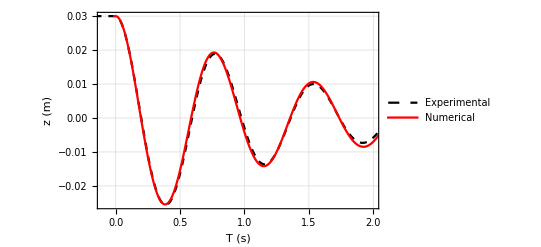

/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_bem/study_benchmark/Kramer2021/comparison_heave.eps

ブイのヒーブ変位の比較

```mathematica
dataExp=Import[FileNameJoin["/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_bem/study_benchmark/Kramer2021/Datafile/Experimental_results/01D_CI95_Normalized.txt"],"Data"];
initCOMZ=("float_COM"/.data)[[1,3]];
dataHeave={#1*Te,H0*#2}&@@@(dataExp[[2;;]]);
dataHeaveFNPF={#1,#2}&@@@(dataSimu[[2;;]]);
shift=0.02

ListPlot[{
dataHeave
,Transpose[{("simulation_time"/.data)-shift,(("float_COM"/.data)[[;;,3]]-initCOMZ+H0)}]
}
,PlotStyle->{{Dashed,Black},{Automatic,Red}}
,PlotRange->{{-0.1,2},All}
,GridLines->Automatic
,FrameLabel->{"T (s)","z (m)"}
,PlotLegends->Placed[LineLegend[{"Experimental","Numerical"},LabelStyle->{15}],{Right,Top}]
,Evaluate[plot2Doption]]
Export[FileNameJoin[{NotebookDirectory[],"comparison_heave.eps"}],%]
Print["ブイのヒーブ変位の比較"]
```